```mathematica
;;;
```

Last updated:   Tue 11 Jul 2023
Author:   Martins Dogo

# Plant Graphs

```mathematica
PlantData["SampleEntities"]
```

{Lonicera maackii f. erubescens,hemp,cosmos,hawthorn,draba,sensitive plant,banana,spruce,oak,tulip,nettle,Balizia leucocalyx,purplestem beggarticks,european centaury,flowering dogwood,paradise plant,venus flytrap,southern california draba,slenderleaf sundew,squirting cucumber,anchored water hyacinth,field horsetail,lompoc yerba santa,funaria moss,Galactia maisiana,meadow geranium,longbranch frostweed,stinkingtoe,cindercone isodendrion,corkwood,arrowleaf falsepickerelweed,heartshape false pickerelweed,Nitella translucens,rice,shortleaf pine,Ptychomitrium fernandesianum,Southern red oak,Rosa viscaria,Irish potato,spanish broom,common dandelion,diamond burbark,lingonberry,wine grape,corn,northern reedgrass,slimstem reedgrass,Frullania kunzei var. kunzei,lanai labordia,simpleleaf chastetree}

```mathematica
pe[e_]:=If[ListQ[e],#["ParentEntity"]&/@e,e["ParentEntity"]]
```

```mathematica
EntityQ[e_]:=If[ListQ[e],
MemberQ[Head/@e,Entity],
Head[e]===Entity]
```

```mathematica
p1=Entity["Plant","Species:CitrusReticulata"];
p2=Entity["Plant","Species:CitrusSinensis"];
plants={p1,p2};
```

```mathematica
gAll=PlantData[#,"TaxonomyGraph"]&/@plants;
```

```mathematica
panelLabel[lbl_]:=Framed[CanonicalName@lbl,FrameMargins->3,Background->Opacity[.9,Lighter[Orange,0.8]],FrameStyle->None,RoundingRadius->5]
```

```mathematica
gu=GraphUnion[Sequence@@gAll,PlotTheme->"GrayColor",EdgeStyle->Thickness[Tiny],EdgeShapeFunction->GraphElementData[{"ShortUnfilledArrow","ArrowSize"->.01}],VertexLabels->Placed["Name",Automatic,panelLabel],VertexSize->.2,GraphLayout->"GravityEmbedding"(*"RadialEmbedding"*),ImageSize->800]
```

-Graphics-

```mathematica
EdgeList[gAll[[1]]]//Short
```

{dicotyledons->Asteridae,dicotyledons->Caryophyllidae,dicotyledons->Dilleniidae,dicotyledons->Hamamelididae,dicotyledons->Magnoliidae,dicotyledons->Rosidae,flowering plants->Liliopsida,flowering plants->dicotyledons,rue family->Acronychia,rue family->aegle,«77»,Rosidae->Rhizophorales,Rosidae->roses, elms, mulberries, hemps...,Rosidae->mistletoes, sandalwoods, olaxes...,Rosidae->maples, citruses, mahogonies, cashews...,vascular plants->seed plants,seed plants->conifers,seed plants->cycads,seed plants->ginkos,seed plants->gnetophytes,seed plants->flowering plants}

```mathematica
DeleteDuplicates@Flatten[EdgeList/@gAll]
```

{dicotyledons->Asteridae,dicotyledons->Caryophyllidae,dicotyledons->Dilleniidae,dicotyledons->Hamamelididae,dicotyledons->Magnoliidae,dicotyledons->Rosidae,flowering plants->Liliopsida,flowering plants->dicotyledons,rue family->Acronychia,rue family->aegle,rue family->agathosma,rue family->torchwood,rue family->angostura,rue family->boronia,rue family->Calodendrum,rue family->sapote,rue family->mexican orange,rue family->citroncirus,rue family->citrus,rue family->clausena,rue family->cneoridium,rue family->australian fuschia,rue family->dictamnus,rue family->eremocitrus,rue family->jopoy,rue family->flindersia,rue family->kumquat,rue family->glycosmis,rue family->helietta,rue family->limonia,rue family->melicope,rue family->microcitrus,rue family->murraya,rue family->corktree,rue family->pilocarpus,rue family->platydesma,rue family->poncirus,rue family->hoptree,rue family->ravenia,rue family->rue,rue family->severinia,rue family->Tetradium,rue family->desertrue,rue family->triphasia,rue family->pricklyash,citrus->key lime,citrus->sour orange,citrus->Citrus hystrix,citrus->rough lemon,citrus->bitter orange,citrus->lemon,citrus->mandarin lime,citrus->Citrus macroptera,citrus->calamondin,citrus->shaddock,citrus->citron,citrus->tangor,citrus->grapefruit,citrus->tangerine,citrus->sweet orange,citrus->tachibana orange,citrus->tangelo,plants->vascular plants,maples, citruses, mahogonies, cashews...->Aceraceae,maples, citruses, mahogonies, cashews...->sumac family,maples, citruses, mahogonies, cashews...->frankincense family,maples, citruses, mahogonies, cashews...->Hippocastanaceae,maples, citruses, mahogonies, cashews...->mahogany family,maples, citruses, mahogonies, cashews...->rue family,maples, citruses, mahogonies, cashews...->Sapindaceae,maples, citruses, mahogonies, cashews...->quassia family,maples, citruses, mahogonies, cashews...->Staphyleaceae,maples, citruses, mahogonies, cashews...->creosote-bush family,Rosidae->Apiales,Rosidae->Celastrales,Rosidae->dogwoods, silk tassels, sour gums, hydrangeas...,Rosidae->spurges, boxwoods, jojobas...,Rosidae->legumes, milkworts, snakeroot, peas...,Rosidae->geraniums,Rosidae->Haloragales,Rosidae->Linales,Rosidae->mezereums, primroses, myrtles...,Rosidae->Podostemales,Rosidae->milkworts, candyroots...,Rosidae->Proteales,Rosidae->Rafflesiales,Rosidae->oleasters, buckthorns, grapes...,Rosidae->Rhizophorales,Rosidae->roses, elms, mulberries, hemps...,Rosidae->mistletoes, sandalwoods, olaxes...,Rosidae->maples, citruses, mahogonies, cashews...,vascular plants->seed plants,seed plants->conifers,seed plants->cycads,seed plants->ginkos,seed plants->gnetophytes,seed plants->flowering plants}

```mathematica
gu//.DirectedEdge->UndirectedEdge
```

-Graphics-

```mathematica
DirectedGraphQ[gu]
```

True

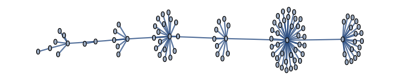

```mathematica
gu2=Graph[EdgeList[gu]/.DirectedEdge->UndirectedEdge]
```

```mathematica
DirectedGraphQ[gu2]
```

False

```mathematica
shortestPath=FindShortestPath[gu2,p1,p2]
```

{tangerine,citrus,sweet orange}

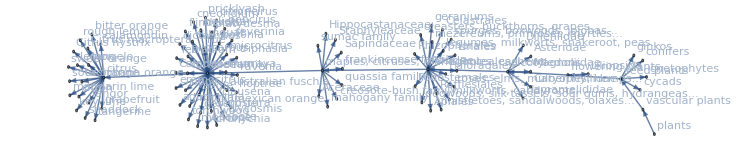

```mathematica
g=GraphUnion[Sequence@@gAll,VertexLabels->Placed["Name",Automatic],VertexSize->.2,EdgeShapeFunction->GraphElementData[{"ShortUnfilledArrow","ArrowSize"->.02}]]
```

```mathematica
HighlightGraph[GraphUnion[Sequence@@gAll,VertexLabels->Placed["Name",Automatic],VertexSize->.25,EdgeShapeFunction->GraphElementData[{"ShortUnfilledArrow","ArrowSize"->.01}]],PathGraph@shortestPath,GraphHighlightStyle->"Thick",PlotTheme->"GrayColor",EdgeStyle->Thin,VertexLabels->Placed["Name",Automatic,panelLabel],GraphLayout->{"LayeredDigraphEmbedding", "Orientation"->Left},AspectRatio->1,ImageSize->800]
```

-Graphics-

```mathematica
HighlightGraph[GraphUnion[Sequence@@gAll,VertexLabels->Placed["Name",Automatic],VertexSize->.25,EdgeShapeFunction->GraphElementData[{"ShortUnfilledArrow","ArrowSize"->.01}]],PathGraph@shortestPath,GraphHighlightStyle->"Thick",PlotTheme->"GrayColor",EdgeStyle->Thin,VertexLabels->Placed["Name",Automatic,panelLabel],GraphLayout->{"RadialEmbedding"},AspectRatio->1,ImageSize->800]
```

-Graphics-

```mathematica
DeleteMissing@NestWhileList[pe,p1,EntityQ]
```

{tangerine,citrus,rue family,maples, citruses, mahogonies, cashews...,Rosidae,dicotyledons,flowering plants,seed plants,vascular plants,plants}

```mathematica
DeleteMissing@NestWhileList[pe,p2,EntityQ]
```

{sweet orange,citrus,rue family,maples, citruses, mahogonies, cashews...,Rosidae,dicotyledons,flowering plants,seed plants,vascular plants,plants}